# DeVylder Approximation for Ruin Probability by USolon

This is an implementation of the DeVylder approximation for ruin probability of a Cramer Lundberg process as discussed in the lecture notes of F. Avram. Notations are taken from there.

From the first three moments of the claim distribution m1, m2 , m3, as well as the safety loading parameter θ and claim arrival rate λ, an approximate ruin probability ψ[u] is computed.

```mathematica
m = {m1,m2,m3};
θ = theta;
λ = lambda;
```

```mathematica
mTilde = m3/(3*m2);
λTilde = (9*(m2)^3)/(2*(m3)^2) * λ;

θTilde = (2*m1*m3)/(3* (m2)^2)*θ;
```

```mathematica
ψ[u_]:= 1/(1+ θTilde)*E^(-(u*θTilde)/(1+θTilde) * 1/mTilde);
```

## Example1

We test first on exponential claims of with survival function F(x) = e^(-αx).

```mathematica
momentSurviv[Fx_,n_,x_] := Module[{s, moment,LF},
LF=LaplaceTransform[n*x^(n-1)*Fx,x,s];
moment=LF /. s-> 0;
moment
]
Fx1 = E^(-α*x);

m = {m1,m2,m3} = {momentSurviv[Fx1,1,x],momentSurviv[Fx1,2,x],momentSurviv[Fx1,3,x]}
λ = lambda =2; (*looks like no apapraent use for lambda in this implementation*)
θ = theta ;
mTilde = m3/(3*m2);
λTilde = (9*(m2)^3)/(2*(m3)^2) * λ; (*no use for this either*)

θTilde = (2*m1*m3)/(3* (m2)^2)*θ;
ψ[x]
```

{1/α,2/α^2,6/α^3}

ⅇ^(-(theta x α)/(1+theta))/(1+theta)

## Constructing a module

We combine parts of the code to a singular function taking as input the moments, theta, and lambda. This module will be used in further examples.

```mathematica
ψ[u_, m1_,m2_,m3_,  θ_,λ_]:= Module[{mTilde, λTilde,θTilde},
mTilde = m3/(3*m2);
λTilde = (9*(m2)^3)/(2*(m3)^2) * λ;

θTilde = (2*m1*m3)/(3* (m2)^2)*θ;
ψ[u]= 1/(1+ θTilde)*E^(-(u*θTilde)/(1+θTilde) * 1/mTilde)
]
```

```mathematica
ψ[x, 1/α, 2/α^2,6/α^3,  θ,λ]
```

ⅇ^(-(theta x α)/(1+theta))/(1+theta)

## Example2

We test now with some hyperexponential claims, starting with sum of 2  exponentials.

From Dufresne-Gerber, ψ[u] =ⅇ^(-3 u)/16+(9 ⅇ^-u)/16

Fx[x] =(3 ⅇ^(-4 x))/4+ⅇ^(-2 x)/4

ρ = 5/8

From PK, ψ[u] = 1/16 ⅇ^(-3 u) (1+9 ⅇ^(2 u))

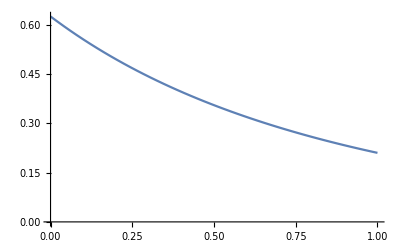

```mathematica
momentSurviv[Fx_,n_,x_] := Module[{s, moment,LF},
LF=LaplaceTransform[n*x^(n-1)*Fx,x,s];
moment=LF /. s-> 0;
moment
]

ruinDirectILT[Fx_,rho_,x_,u_]:= Module[{s,L1,f,m1, Lf, fe,Fe,Lrui},
f[x] = -D[Fx[x],x];
m1 = Integrate[Fx[x],{x,0,∞}];
Lf = LaplaceTransform[Fx[x],x,s];
fe = Lf/m1;
Fe=Factor[((1-fe)/s)];
Lrui=rho*Fe/(1-rho*fe);
L1 =InverseLaplaceTransform[Lrui,s,u]
]

r={1,3};β={2,4}; n = Length[r];
varC=Table[Symbol["varC"<>ToString[i]],{i,1,n}];
condC = Table[∑_(k=1)^(k=n) varC[[k]]/(β[[i]]- r[[k]]) ==1/β[[i]],{i,n}];
s = Solve[condC, varC];
c=Flatten[varC/.{s}];
ρ = Total[c];
θ = ρ^(-1) -1;
varA=Table[Symbol["varA"<>ToString[i]],{i,1,n}];
condA = Table[∑_(i=1)^n varA[[i]]/(β[[i]]- r[[k]]) ==1 ,{k,n}];
s = Solve[condA, varA];
a=Flatten[varA/.{s}];
a = a/Total[a];

Print["From Dufresne-Gerber, ψ[u] =",ψ[u_] = ∑_(i=1)^n c[[i]]*E^(-r[[i]]*u)];
Print["Fx[x] =",Fx[x_] = ∑_(i=1)^(i=n) a[[i]]*E^(-β[[i]]*x)];
Print["ρ = ", ρ]
Print["From PK, ψ[u] = ",ruinDirectILT[Fx, ρ, x, u]]
Plot[ψ[u], {u,0,1}, PlotRange->{{0,1},{0, ρ}}]
```

{5/16,7/32,33/128}

3/5

From DeVylder approx, ψ[u] = 1/16 ⅇ^(-3 u) (1+9 ⅇ^(2 u))

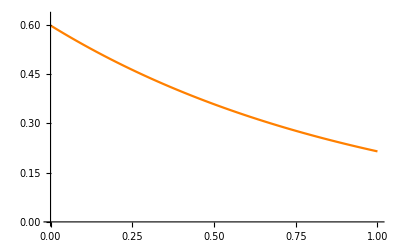

```mathematica
Fx1 = Fx[x];
m = {m1,m2,m3} = {momentSurviv[Fx1,1,x],momentSurviv[Fx1,2,x],momentSurviv[Fx1,3,x]}
ρ = Total[c];
θ = ρ^(-1) -1

mTilde = m3/(3*m2);

θTilde = (2*m1*m3)/(3* (m2)^2)*θ;
ψDV[u_]:= 1/(1+ θTilde)*E^(-(u*θTilde)/(1+θTilde) * 1/mTilde)
Print["From DeVylder approx, ψ[u] = ",ruinDirectILT[Fx, ρ, x, u]]
Plot[ψDV[u], {u,0,1}, PlotRange->{{0,1},{0, ρ}}, PlotStyle->{Orange}]
```

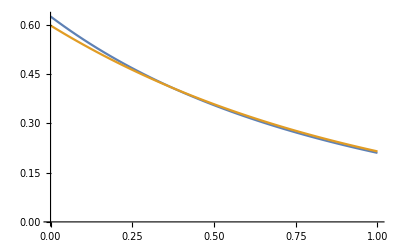

From DeVylder approx, ψ[u] = 1/16 ⅇ^(-3 u) (1+9 ⅇ^(2 u))

From PK, ψ[u] = 1/16 ⅇ^(-3 u) (1+9 ⅇ^(2 u))

```mathematica
Plot[{ψ[u], ψDV[u]}, {u,0,1}, PlotRange->{{0,1},{0, ρ}}]
Print["From DeVylder approx, ψ[u] = ",ruinDirectILT[Fx, ρ, x, u]]
Print["From PK, ψ[u] = ",ruinDirectILT[Fx, ρ, x, u]]
```

## Example 3

Another hyperexponential claim, sum of 3 exponentials.

From Dufresne-Gerber, ψ[u] =(8 ⅇ^(-10 u))/81+ⅇ^(-5 u)/12+(175 ⅇ^-u)/324

Fx[x] =(100 ⅇ^(-15 x))/117+(5 ⅇ^(-6 x))/63+(6 ⅇ^(-2 x))/91

ρ = 13/18

From PK, ψ[u] = 1/324 ⅇ^(-10 u) (32+27 ⅇ^(5 u)+175 ⅇ^(9 u))

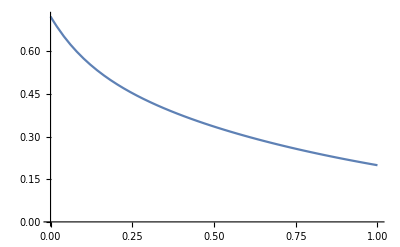

```mathematica
r={1,5,10};β={2,6,15}; n = Length[r];
varC=Table[Symbol["varC"<>ToString[i]],{i,1,n}];
condC = Table[∑_(k=1)^(k=n) varC[[k]]/(β[[i]]- r[[k]]) ==1/β[[i]],{i,n}];
s = Solve[condC, varC];
c=Flatten[varC/.{s}];
ρ = Total[c];
θ = ρ^(-1) -1;
varA=Table[Symbol["varA"<>ToString[i]],{i,1,n}];
condA = Table[∑_(i=1)^n varA[[i]]/(β[[i]]- r[[k]]) ==1 ,{k,n}];
s = Solve[condA, varA];
a=Flatten[varA/.{s}];
a = a/Total[a];

Print["From Dufresne-Gerber, ψ[u] =",ψ[u_] = ∑_(i=1)^n c[[i]]*E^(-r[[i]]*u)];
Print["Fx[x] =",Fx[x_] = ∑_(i=1)^(i=n) a[[i]]*E^(-β[[i]]*x)];
Print["ρ = ", ρ]
Print["From PK, ψ[u] = ",ruinDirectILT[Fx, ρ, x, u]]
Plot[ψ[u], {u,0,1}, PlotRange->{{0,1},{0, ρ}}]
```

{13/126,17/378,67/1260}

5/13

From DeVylder approx, ψ[u] = 1/324 ⅇ^(-10 u) (32+27 ⅇ^(5 u)+175 ⅇ^(9 u))

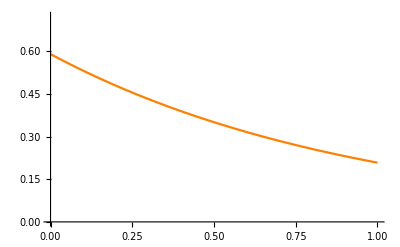

```mathematica
Fx1 = Fx[x];
m = {m1,m2,m3} = {momentSurviv[Fx1,1,x],momentSurviv[Fx1,2,x],momentSurviv[Fx1,3,x]}
ρ = Total[c];
θ = ρ^(-1) -1

mTilde = m3/(3*m2);

θTilde = (2*m1*m3)/(3* (m2)^2)*θ;
ψDV[u_]:= 1/(1+ θTilde)*E^(-(u*θTilde)/(1+θTilde) * 1/mTilde)
Print["From DeVylder approx, ψ[u] = ",ruinDirectILT[Fx, ρ, x, u]]
Plot[ψDV[u], {u,0,1}, PlotRange->{{0,1},{0, ρ}}, PlotStyle->{Orange}]
```

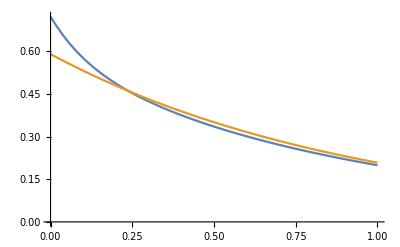

From DeVylder approx, ψ[u] = 1/324 ⅇ^(-10 u) (32+27 ⅇ^(5 u)+175 ⅇ^(9 u))

From PK, ψ[u] = 1/324 ⅇ^(-10 u) (32+27 ⅇ^(5 u)+175 ⅇ^(9 u))

```mathematica
Plot[{ψ[u], ψDV[u]}, {u,0,1}, PlotRange->{{0,1},{0, ρ}}]
Print["From DeVylder approx, ψ[u] = ",ruinDirectILT[Fx, ρ, x, u]]
Print["From PK, ψ[u] = ",ruinDirectILT[Fx, ρ, x, u]]
```

## Example 4

Another hyperexponential claim, sum of 5 exponentials.

From Dufresne-Gerber, ψ[u] =(245 ⅇ^(-9 u))/32768+(135 ⅇ^(-7 u))/8192+(567 ⅇ^(-5 u))/16384+(735 ⅇ^(-3 u))/8192+(19845 ⅇ^-u)/32768

Fx[x] =(63 ⅇ^(-10 x))/128+(7 ⅇ^(-8 x))/32+(9 ⅇ^(-6 x))/64+(3 ⅇ^(-4 x))/32+(7 ⅇ^(-2 x))/128

ρ = 193/256

From PK, ψ[u] = (ⅇ^(-9 u) (245+540 ⅇ^(2 u)+1134 ⅇ^(4 u)+2940 ⅇ^(6 u)+19845 ⅇ^(8 u)))/32768

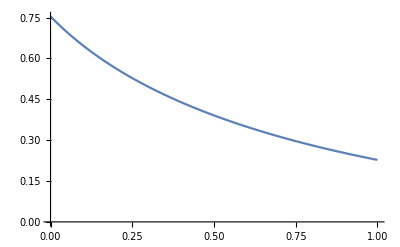

```mathematica
r={1,3,5,7,9};β={2,4,6,8,10}; n = Length[r];
varC=Table[Symbol["varC"<>ToString[i]],{i,1,n}];
condC = Table[∑_(k=1)^(k=n) varC[[k]]/(β[[i]]- r[[k]]) ==1/β[[i]],{i,n}];
s = Solve[condC, varC];
c=Flatten[varC/.{s}];
ρ = Total[c];
θ = ρ^(-1) -1;
varA=Table[Symbol["varA"<>ToString[i]],{i,1,n}];
condA = Table[∑_(i=1)^n varA[[i]]/(β[[i]]- r[[k]]) ==1 ,{k,n}];
s = Solve[condA, varA];
a=Flatten[varA/.{s}];
a = a/Total[a];

Print["From Dufresne-Gerber, ψ[u] =",ψ[u_] = ∑_(i=1)^n c[[i]]*E^(-r[[i]]*u)];
Print["Fx[x] =",Fx[x_] = ∑_(i=1)^(i=n) a[[i]]*E^(-β[[i]]*x)];
Print["ρ = ", ρ]
Print["From PK, ψ[u] = ",ruinDirectILT[Fx, ρ, x, u]]
Plot[ψ[u], {u,0,1}, PlotRange->{{0,1},{0, ρ}}]
```

{193/1280,1627/25600,60649/1024000}

63/193

From DeVylder approx, ψ[u] = (ⅇ^(-9 u) (245+540 ⅇ^(2 u)+1134 ⅇ^(4 u)+2940 ⅇ^(6 u)+19845 ⅇ^(8 u)))/32768

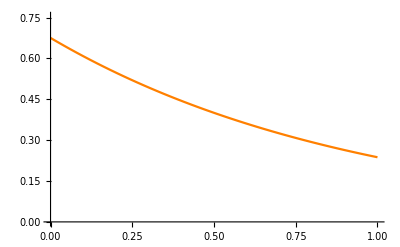

```mathematica
Fx1 = Fx[x];
m = {m1,m2,m3} = {momentSurviv[Fx1,1,x],momentSurviv[Fx1,2,x],momentSurviv[Fx1,3,x]}
ρ = Total[c];
θ = ρ^(-1) -1

mTilde = m3/(3*m2);

θTilde = (2*m1*m3)/(3* (m2)^2)*θ;
ψDV[u_]:= 1/(1+ θTilde)*E^(-(u*θTilde)/(1+θTilde) * 1/mTilde)
Print["From DeVylder approx, ψ[u] = ",ruinDirectILT[Fx, ρ, x, u]]
Plot[ψDV[u], {u,0,1}, PlotRange->{{0,1},{0, ρ}}, PlotStyle->{Orange}]
```

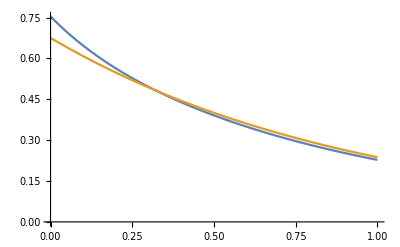

From DeVylder approx, ψ[u] = (ⅇ^(-9 u) (245+540 ⅇ^(2 u)+1134 ⅇ^(4 u)+2940 ⅇ^(6 u)+19845 ⅇ^(8 u)))/32768

From PK, ψ[u] = (ⅇ^(-9 u) (245+540 ⅇ^(2 u)+1134 ⅇ^(4 u)+2940 ⅇ^(6 u)+19845 ⅇ^(8 u)))/32768

```mathematica
Plot[{ψ[u], ψDV[u]}, {u,0,1}, PlotRange->{{0,1},{0, ρ}}]
Print["From DeVylder approx, ψ[u] = ",ruinDirectILT[Fx, ρ, x, u]]
Print["From PK, ψ[u] = ",ruinDirectILT[Fx, ρ, x, u]]
```